```mathematica
a ={ 0.1,0.25,0.5,0.75,1.0};
```

```mathematica
Pz = {0.75,0.7,0.521,0.383,0.295};
```

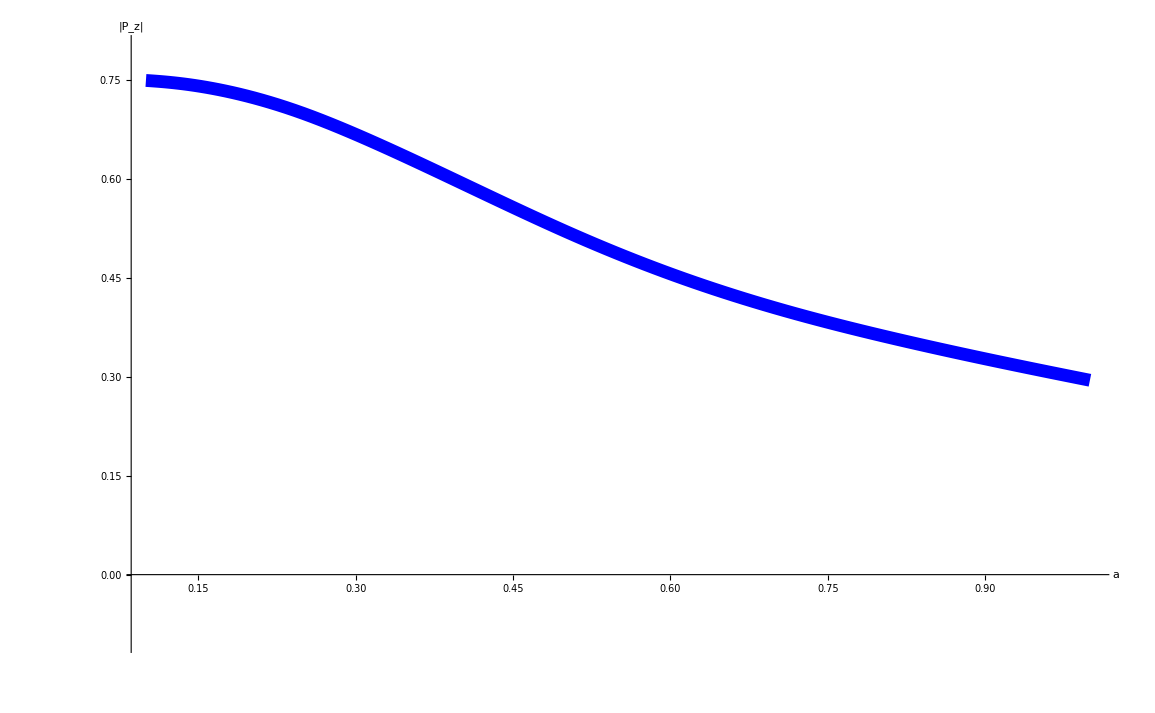

```mathematica
ListLinePlot[Table[{a[[k]],Pz[[k]]},{k,1,Length[a]}],InterpolationOrder->3,TicksStyle->Directive[Black,FontFamily->"Latin Modern Roman",36],AxesLabel->{Style["a",FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->48],Style["|P_z|",FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->48]},PlotStyle->Directive[Blue,Thickness[0.008]],PlotRange->{All,{-0.1,0.8}}]
```